```mathematica
(*This plots the subhalo mass funcation from Daneng *)
```

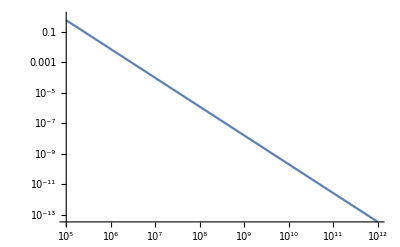

```mathematica
LogLogPlot[ (2*(10^-10)) (x/(10^10))^(-1.89) , {x,10^5, 10^12} ]
```

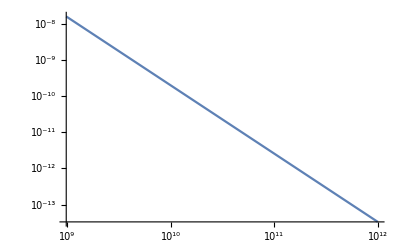

```mathematica
LogLogPlot[ (2*(10^-10)) (x/(10^10))^(-1.89) , {x,0, 10^12} ]
```

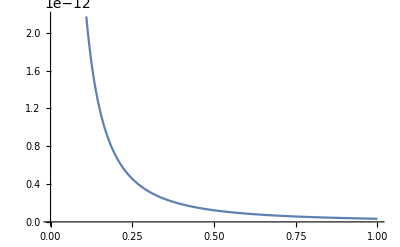

```mathematica
Plot[ (2*(10^-10)) (x/(10^10))^(-1.89) , {x,0, 10^12} ]
```

```mathematica
(*So this area under the curve does not converge but there is a lower mass limit given by the PBH paper https://arxiv.org/pdf/1604.05349.pdf. However this lower limit comes from the temperature at inflation so it doesn't really make sense for black holes forming later on from SIDM. The limit is 5*10^14 g = 2.5*10^-19 solar masses. Daneng assumed a lower mass limit of 1 solar mass for his microlensing calucation however since the LSST constraints are much lower, it makes sense to look at lower mass objects*)
```

```mathematica
Plot[ (2*(10^-10)) (x/(10^10))^(-1.89) , {x,2.5*10^-19, 10^12} ]
```

-Graphics-

```mathematica
(*Now we can create a funcation to calculate the intergal of the mass funcation which give the number of objects in the mass range. The smaller this mass range the less total mass included which make it a smaller percent of the the total dark matter mass in the milkway  *)
```

```mathematica
MassSH[LLimit_,ULimit_]:=(2*(10^-10))*Integrate[(x/(10^10))^(-1.89),{x,LLimit, ULimit}]
```

```mathematica
(*Testing the funcation*)
```

```mathematica
MassSH[10^-12,10^12]
```

8.54358×10^19

```mathematica
(2*(10^-10))*Integrate[(x/(10^10))^(-1.89),{x,10^-12,10^12}]
```

8.54358×10^19

```mathematica
(*Here I wrote a loop to integrate over the mass range 10^-6 to 10^3.1 
This range is where the LSST constraints are the lowest. The step size is 10^0.1 which is fairly small. I then take this array into python to make the plots and calcaute the dark matter fraction for each mass range. This data made my lastest plots *)
```

```mathematica
Results={};
For[i=-6,i<=3,i+=0.1,lowerLimit=10^i;
upperLimit=10^(i+0.1);
Result=MassSH[lowerLimit,upperLimit]
;
AppendTo[Results,{lowerLimit,Result,upperLimit}];]

Print[Results];
```

{{1/1000000,7.23611×10^13,1.25893×10^-6},{1.25893×10^-6,5.89529×10^13,1.58489×10^-6},{1.58489×10^-6,4.80292×10^13,1.99526×10^-6},{1.99526×10^-6,3.91296×10^13,2.51189×10^-6},{2.51189×10^-6,3.1879×10^13,3.16228×10^-6},{3.16228×10^-6,2.5972×10^13,3.98107×10^-6},{3.98107×10^-6,2.11595×10^13,5.01187×10^-6},{5.01187×10^-6,1.72387×10^13,6.30957×10^-6},{6.30957×10^-6,1.40445×10^13,7.94328×10^-6},{7.94328×10^-6,1.14421×10^13,0.00001},{0.00001,9.32192×10^12,0.0000125893},{0.0000125893,7.59461×10^12,0.0000158489},{0.0000158489,6.18736×10^12,0.0000199526},{0.0000199526,5.04087×10^12,0.0000251189},{0.0000251189,4.10682×10^12,0.0000316228},{0.0000316228,3.34584×10^12,0.0000398107},{0.0000398107,2.72587×10^12,0.0000501187},{0.0000501187,2.22078×10^12,0.0000630957},{0.0000630957,1.80928×10^12,0.0000794328},{0.0000794328,1.47403×10^12,0.0001},{0.0001,1.2009×10^12,0.000125893},{0.000125893,9.78375×10^11,0.000158489},{0.000158489,7.97086×10^11,0.000199526},{0.000199526,6.4939×10^11,0.000251189},{0.000251189,5.29061×10^11,0.000316228},{0.000316228,4.31028×10^11,0.000398107},{0.000398107,3.5116×10^11,0.000501187},{0.000501187,2.86092×10^11,0.000630957},{0.000630957,2.3308×10^11,0.000794328},{0.000794328,1.89891×10^11,0.001},{0.001,1.54705×10^11,0.00125893},{0.00125893,1.26039×10^11,0.00158489},{0.00158489,1.02685×10^11,0.00199526},{0.00199526,8.36576×10^10,0.00251189},{0.00251189,6.81562×10^10,0.00316228},{0.00316228,5.55271×10^10,0.00398107},{0.00398107,4.52382×10^10,0.00501187},{0.00501187,3.68558×10^10,0.00630957},{0.00630957,3.00265×10^10,0.00794328},{0.00794328,2.44628×10^10,0.01},{0.01,1.99299×10^10,0.0125893},{0.0125893,1.6237×10^10,0.0158489},{0.0158489,1.32283×10^10,0.0199526},{0.0199526,1.07772×10^10,0.0251189},{0.0251189,8.78022×10^9,0.0316228},{0.0316228,7.15328×10^9,0.0398107},{0.0398107,5.82781×10^9,0.0501187},{0.0501187,4.74794×10^9,0.0630957},{0.0630957,3.86817×10^9,0.0794328},{0.0794328,3.15141×10^9,0.1},{0.1,2.56747×10^9,0.125893},{0.125893,2.09173×10^9,0.158489},{0.158489,1.70414×10^9,0.199526},{0.199526,1.38837×10^9,0.251189},{0.251189,1.13111×10^9,0.316228},{0.316228,9.21521×10^8,0.398107},{0.398107,7.50767×10^8,0.501187},{0.501187,6.11653×10^8,0.630957},{0.630957,4.98317×10^8,0.794328},{0.794328,4.05981×10^8,1.},{1.,3.30754×10^8,1.25893},{1.25893,2.69467×10^8,1.58489},{1.58489,2.19536×10^8,1.99526},{1.99526,1.78857×10^8,2.51189},{2.51189,1.45715×10^8,3.16228},{3.16228,1.18715×10^8,3.98107},{3.98107,9.67176×10^7,5.01187},{5.01187,7.87962×10^7,6.30957},{6.30957,6.41956×10^7,7.94328},{7.94328,5.23004×10^7,10.},{10.,4.26094×10^7,12.5893},{12.5893,3.47141×10^7,15.8489},{15.8489,2.82817×10^7,19.9526},{19.9526,2.30412×10^7,25.1189},{25.1189,1.87718×10^7,31.6228},{31.6228,1.52934×10^7,39.8107},{39.8107,1.24596×10^7,50.1187},{50.1187,1.01509×10^7,63.0957},{63.0957,8.27×10^6,79.4328},{79.4328,6.7376×10^6,100.},{100.,5.48915×10^6,125.893},{125.893,4.47204×10^6,158.489},{158.489,3.64339×10^6,199.526},{199.526,2.96828×10^6,251.189},{251.189,2.41827×10^6,316.228},{316.228,1.97018×10^6,398.107},{398.107,1.60511×10^6,501.187},{501.187,1.30769×10^6,630.957},{630.957,1.06538×10^6,794.328},{794.328,867971.,1000.},{1000.,707140.,1258.93}}

```mathematica
(*I tried in the beginning to just integrate analytically but it was negative plus there is always a unknown constant which could really shifting the number of objects. I was assuming it was zero but there are lots of options and I'm not sure what is phyiscally motivated. When I talked to Daneng he said to integrate numerically to avoid this issue *)
```

```mathematica
(2*(10^-10))*Integrate[(x/(10^10))^(-1.89),x]
```

-(1.78501×10^9)/x^0.89

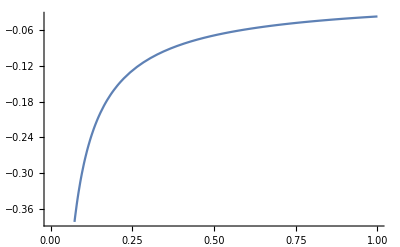

```mathematica
Plot [-(1.785007269043325*^9)/x^0.8899999999999999,{x,0,10^12}]
```

```mathematica
(*For example if C=1 *)
```

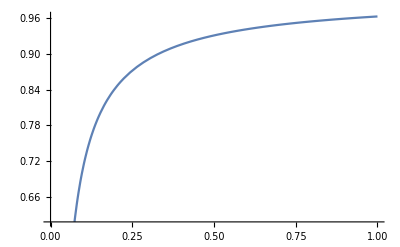

```mathematica
Plot [-(1.785007269043325*^9)/x^0.8899999999999999+ 1,{x,0,10^12}]
```

```mathematica
(*But numerically, we get the binning issue I mentioned in our last meeting. https://arxiv.org/pdf/1604.05349.pdf for milky way mass.  To demonstrate *)
```

```mathematica
MassSH[10^-12,10^12]  (* the number of objects between 10^-12 to 10 ^12 solar mass *)
```

8.54358×10^19

```mathematica
(*find the average mass in the range *)
```

```mathematica
N[((10^-12 + 10^12) /2 )]
```

5.×10^11

```mathematica
(* Multiply the number of objects by the average mass in the range and divide by the total mass in milkway to get dark matter fraction.  1.08*10^12 solar mass
https://arxiv.org/abs/1911.04557  *)
```

```mathematica
((5*10^11 )* (8.543581939787774 * 10 ^19 )) /  (1.08*10^12 )
```

3.95536×10^19

```mathematica
(*Since this is a huge mass range, we get a huge dark matter fraction that doesn't make sense physically, Next for a smaller mass range *)
```

```mathematica
MassSH[10^-5,10^-4]
```

4.38274×10^13

```mathematica
N[((10^-4 + 10^-5) /2 )]
```

```mathematica
0.000055
```

```mathematica
ScientificForm[(0.000055)* (4.382737052259887*10^13 ) /  (1.08*10^12 )] (*Dark Matter Fraction*)
```

2.23195×10^-3

```mathematica
(*For an even smaller mass range *)
```

```mathematica
MassSH[10^-4,10^-3.9]
```

1.2009×10^12

```mathematica
N[((10^-4 + 10^-3.9) /2 )]
```

0.000112946

```mathematica
ScientificForm[(1.2008959152320251*10^12)* (0.00011294627058970838 ) /  (1.08*10^12 ) ]
```

1.2559×10^-4

```mathematica
(*So it makes sense to make mathematically that the smaller the mass range, even though there could be a high number of objects, results in a smaller of dark matter fraction, but this leaves the issues of how to apply it properly to the exist constraints   *)
```

```mathematica
(*In reviewing Primordial Black Holes as Dark Matter https://arxiv.org/abs/1607.06077 section C on page 5 and section IV.    *)
```

```mathematica
(*Using equation 11  rho(M) =M^2 * dn/dM, rho is the mass density  * )
```

```mathematica
rho[x_] := (x)^2 * (2*(10^-10)) (x/(10^10))^(-1.89)
```

```mathematica
rho[10^0.1]
```

1.62941×10^9

```mathematica
(*And to get the dark matter fraction *)
```

```mathematica
f[x_] = rho[x] /  (1.08*10^12 )
```

0.00233134/x^1.89

```mathematica
f[10^2]
```

3.86907×10^-7

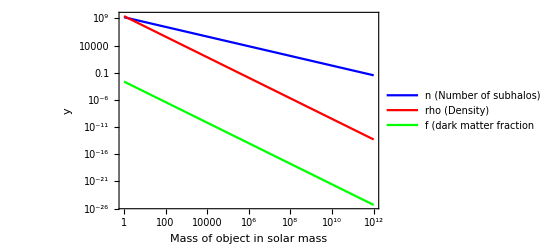

```mathematica
(*Equation 10 for number of objects *)
n[M_] = M * (2*(10^-10)) (M/(10^10))^(-1.89) ;
(*Plot n and rho on log-log scale as the paper suggests *)
LogLogPlot[{n[x],rho[x],f[x]},{x,1,10^12},PlotStyle->{Blue,Red, Green},PlotLegends->{"n (Number of subhalos)","rho (Density)", "f (dark matter fraction"},Frame->True,FrameLabel->{"Mass of object in solar mass","y"},PlotRange->{{0,10^12},Automatic}]
```

```mathematica
(*this follows the equations in the paper, but we never integrated so I think this is just an approximation for when the bin size is equal to M and a power law mass funcation. This can be plotted on LSST constaints which I will do if you think this is correct  *)
```

```mathematica
(*note: this is all done with the subhalo mass funcationm, can repeat with the black hole mass funcation too *)

(* Related discussion in Ref.[35],  https://arxiv.org/pdf/1604.05349.pdf section 3 page 9, shows type of non monochromatic mass funcations would be possible not how to transform constraints *)
```